#### Preamble

```mathematica
(*ClearAll["Global`*"]*)
ClearAll@@{$Context<>"*"}
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
$HistoryLength=5;
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
fs = 11;
fsLabel=13; 
th = AbsoluteThickness[1.5];
```

/home/jonathan/Dropbox/WorkWithAlejandro/3.- COMSOL-Mie

```mathematica
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
graphsOpts:= {BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black}
```

### Useful functions (Importing Data, Graphing, Derivatives, Extrema Pints)

#### Import data

```mathematica
fecha[]:=Module[{y,m,d,h,min,s}, {y,m,d,h,min,s}=Date[];
"==="<>ToString[y]<>"/"<>ToString[m]<>"/"<>ToString[d]<>"---"<>ToString[h]<>":"<>ToString[min]<>":"<>ToString[s]<>"===\n"]
```

```mathematica
importData[list_]:=Module[{i,long1={}},
For[i=1,i≤ Length[list],i++,
	If[Length[list[[i]]]==1,AppendTo[long1,i]]];
AppendTo[long1,Length[list]+1];
Table[list[[long1[[i]]+3;;long1[[i+1]]-1]],{i,1,Length[long1]-1}]]
```

#### graphing

```mathematica
Options[plotGrid]={ImagePadding->50};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

```mathematica
Options[linearTicks]={"NumberLabels"-> True};
linearTicks[interval_,step_,divisions_,OptionsPattern[]]:=Module[{withLabels,smallTicks,h,labels,i},
h= step/divisions;
labels=If[OptionValue["NumberLabels"],i,Null];
withLabels=Table[{i,labels,{.02,0}},{i,interval[[1]],interval[[2]],step}];
smallTicks = Table[{i,Null},{i,interval[[1]]-10*h,interval[[2]]+10*h,h}];
Join[withLabels,smallTicks]
]
hcTicksDecimals[interval_,noLabels_,divisions_,takeLabels_]:=Module[{withLabels,smallTicks,hc},
hc = (4.13567*^-15)*(3*^17);
smallTicks={hc/#,Null}&/@FindDivisions[hc/{interval[[2]],interval[[1]]},divisions*noLabels];
withLabels ={hc/#,ToString[NumberForm[N@#,{2,1}]],{.02,0}}&/@FindDivisions[hc/{interval[[2]],interval[[1]]},noLabels];
withLabels=Flatten@@{Take[withLabels,{#}]&/@takeLabels,1};
Join[withLabels,smallTicks]
]
hcTicksInt[interval_,noLabels_,divisions_,takeLabels_]:=Module[{withLabels,smallTicks,hc},
hc = (4.13567*^-15)*(3*^17);
smallTicks={hc/#,Null}&/@FindDivisions[hc/{interval[[2]],interval[[1]]},divisions*noLabels];
withLabels ={hc/#,ToString[IntegerPart@N@#],{.02,0}}&/@FindDivisions[hc/{interval[[2]],interval[[1]]},noLabels];
withLabels=Flatten@@{Take[withLabels,{#}]&/@takeLabels,1};
Join[withLabels,smallTicks]
]
```

#### Derivatives O(h^4)

```mathematica
df[list_]:=Module[{xlist, ylist}, (*1st order derivative, one variable, with O(h^4) *)
xlist=list[[All,1]];
ylist = list[[All,2]];
	Table[{xlist[[i]],(1/12 ylist[[i-2]]-2/3 ylist[[i-1]]+2/3 ylist[[i+1]]-1/12 ylist[[i+2]])/(xlist[[i+1]]-xlist[[i]])},{i,3,Length[xlist]-2}]]
ddf[list_]:=Module[{xlist, ylist}, (*2st order derivative, one variable, with O(h^4) *)
xlist=list[[All,1]];
ylist = list[[All,2]];Table[{xlist[[i]],(-1/12 ylist[[i-2]]+4/3 ylist[[i-1]]-5/2 ylist[[i]]+4/3 ylist[[i+1]]-1/12 ylist[[i+2]])/(xlist[[i+1]]-xlist[[i]])^2},{i,3,Length[xlist]-2}]]
```

#### Extrema - Points

```mathematica
(*Golden ration sectioning for MAXIMA
 The analytcal expresion of the funtion is needed and it depends only in one variable There has to be a extrema value!! Otherwise the result is one side of the interval
With this version of the code, the interval could be a Pair or a list of Pairs*)
grMax[func_, interval_]:=Module[{gr =  .5*(Sqrt[5.]+1) ,a,b,c,d,i,extrema = {},err=1*^-8}, 
If[Length[Dimensions[interval]]==1,
	{a,b}= interval;
	c = b - (b-a)/gr;
	d = a + (b-a)/gr;
	While[Abs[c-d]> err,
		 If[func[c]>func[d], b = d, a= c];
		c = b - (b-a)/gr;
		d = a + (b-a)/gr];
	extrema = .5*(a + b),
	For[i=1,i≤ Length[Dimensions[interval]],i++,
		{a,b} = interval[[i]];
		c = b - (b-a)/gr;
		d = a + (b-a)/gr;
		While[Abs[c-d]> err,
			 If[func[c]>func[d], b = d, a= c];
			c = b - (b-a)/gr;
			d = a + (b-a)/gr];
		AppendTo[extrema,.5*(a + b)]]];
extrema]
```

```mathematica
(*Golden ration sectioning for MINIMA
 The analytcal expresion of the funtion is needed and it depends only in one variable There has to be a extrema value!! Otherwise the result is one side of the interval
With this version of the code, the interval could be a Pair or a list of Pairs*)
grMin[func_, interval_]:=Module[{gr =  .5*(Sqrt[5.]+1) ,a,b,c,d,i,extrema = {},err=1*^-8}, 
If[Length[Dimensions[interval]]==1,
	{a,b}= interval;
	c = b - (b-a)/gr;
	d = a + (b-a)/gr;
	While[Abs[c-d]> err,
		 If[func[c]<func[d], b = d, a= c];
		c = b - (b-a)/gr;
		d = a + (b-a)/gr];
	extrema = .5*(a + b),
	For[i=1,i≤ Length[Dimensions[interval]],i++,
		{a,b} = interval[[i]];
		c = b - (b-a)/gr;
		d = a + (b-a)/gr;
		While[Abs[c-d]> err,
			 If[func[c]<func[d], b = d, a= c];
			c = b - (b-a)/gr;
			d = a + (b-a)/gr];
		AppendTo[extrema,.5*(a + b)]]];
extrema]
```

```mathematica
(* A posible solution to know if there's a minima or not, is by  finding a change of sing into the given interval of the 1st derivative.  Since we are already doing this, we can determinate of the extrema it's a minimum or maxima via the 2nd derivative 
		---------NEEDS df and ddf DEFINED IN THE Derivative SECTION----------
*)
intExtremaSPP[func_, interval_,h_]:= Module[{xf,dfunc,ddfunc,rootsIntMax={},rootsIntMin={},i}, 
(*interval = {a,b}, h is a number. \\ {maxs, mins}= intExtrema[f,{a,b}, h]*)
xf = Table[{x,func[x]},{x,interval[[1]],interval[[2]],(interval[[2]]-interval[[1]])/h}];	(*CAMBIAR POR h luego*)
dfunc=df[xf];
ddfunc = ddf[xf];
For[i=1,i≤ Length[dfunc]-1, i++,
	If[dfunc[[i,2]]*dfunc[[i+1,2]]≤ 0, 
		If[ddfunc[[i,2]]<0,
			AppendTo[rootsIntMax,{dfunc[[i,1]],dfunc[[i+1,1]]}],  
			AppendTo[rootsIntMin,{dfunc[[i,1]],dfunc[[i+1,1]]}]]]];
{rootsIntMax,rootsIntMin}]
```

```mathematica
(* It's the same but it improves the calculation of a function f(x,y)=z*)intExtrema[func_, interval_,h_]:= Module[{xf,xfS,xfP,dfuncS,ddfuncS,rootsIntMaxS={},rootsIntMinS={},dfuncP,ddfuncP,rootsIntMaxP={},rootsIntMinP={},i}, 
(*interval = {a,b}, h is a number. \\ {maxs, mins}= intExtrema[f,{a,b}, h]*)
xf = ParallelTable[Flatten[{x,func[x]}],{x,interval[[1]],interval[[2]],(interval[[2]]-interval[[1]])/h}];(*CAMBIAR POR h luego*)
xfS=xf[[All,{1,2}]]; xfP = xf[[All,{1,3}]];	
dfuncS=df[xfS];dfuncP=df[xfP];
ddfuncS = ddf[xfS];ddfuncP = ddf[xfP];
For[i=1,i≤ Length[dfuncS]-1, i++,
	If[dfuncS[[i,2]]*dfuncS[[i+1,2]]≤ 0, 
		If[ddfuncS[[i,2]]<0,
			AppendTo[rootsIntMaxS,{dfuncS[[i,1]],dfuncS[[i+1,1]]}],  
			AppendTo[rootsIntMinS,{dfuncS[[i,1]],dfuncS[[i+1,1]]}]]]];
For[i=1,i≤ Length[dfuncP]-1, i++,
	If[dfuncP[[i,2]]*dfuncP[[i+1,2]]≤ 0, 
		If[ddfuncP[[i,2]]<0,
			AppendTo[rootsIntMaxP,{dfuncP[[i,1]],dfuncP[[i+1,1]]}],  
			AppendTo[rootsIntMinP,{dfuncP[[i,1]],dfuncP[[i+1,1]]}]]]];
{rootsIntMaxS,rootsIntMinS,rootsIntMaxP,rootsIntMinP}]
```

#### Color Bars

```mathematica
DensityPlot[x,{x,0,1},{y,0,1},BaseStyle-> texStyle,FrameStyle-> Black,FrameTicks->{{None,None},{None,All}},AspectRatio->1/50,PlotRange->All,ColorFunction->"Rainbow",PlotPoints->40,PlotRangePadding->None,ImageSize->2*{500,20}]
Export["bar_h.svg",%]
(*
DensityPlot[y,{x,0,1},{y,0,1},BaseStyle-> texStyle,FrameTicks->{{None,All},{None,None}},AspectRatio->20,PlotRange->All,ColorFunction->"Rainbow",PlotPoints->40,PlotRangePadding->None,PlotLabel->MaTeX["I/I_0",FontSize->fsLabel],ImageSize->{40,190}]*)
fs = 11
```

-Graphics-

bar_h.svg

11

## Data of materials

```mathematica
h = 4.135668*^-15 (*eV s*);c = 3*^17 (*nm s^-1*);hc = h*c;
materialdata = FileNames["~/Dropbox/RefIndexDataBase/*"]
```

{~/Dropbox/RefIndexDataBase/Ag_nm.csv,~/Dropbox/RefIndexDataBase/Au_2.csv,~/Dropbox/RefIndexDataBase/BK7.csv,~/Dropbox/RefIndexDataBase/Corning.csv,~/Dropbox/RefIndexDataBase/H2O.csv,~/Dropbox/RefIndexDataBase/Si.csv}

The visible range is from 400nm to 780nm  (Handbook of Spectroscopy.Edited by Günter Gauglitz and Tuan Vo-Dinh, Copyright c 2003 WILEY-VCH Verlag GmbH& Co.KGaA,Weinheim, ISBN 3-527-29782-0)
that is in eV

## Ag: P. B. Johnson and R. W. Christy. Optical Constants of the Noble Metals, Phys. Rev. B 6, 4370-4379 (1972)

```mathematica
nAg = Import[materialdata[[1]],"Data"]; (* {λ [nm], n, κ} donde N = n+iκ y ε = N^2   *) 
nAg = Drop[nAg,1];

nAgFunc=Interpolation[nAg/.{λ_,n_, κ_}-> {λ,n+I κ}];
εAgFunc=Interpolation[nAg/.{λ_,n_, κ_}-> {λ,(n+I κ)^2}];

dummy1=Interpolation[nAg/.{λ_,n_, κ_}-> {λ,n^2-κ^2},Method->"Spline"];
dummy2=Interpolation[nAg/.{λ_,n_, κ_}-> {λ,2*n*κ},Method->"Spline"]
εAgFuncSpline[x_]:=dummy1[x]+I*dummy2[x]
```

InterpolatingFunction[…]

## Au: Johnson, P. B.; Christy, R. W. (1972). “Optical Constants of the Noble Metals”. Physical Review B. 6 (12): 4370–4379

```mathematica
nAueV = Import[materialdata[[2]],"Data"] ;(*1 es Ag, 2 es Au, 3 es en H2O en nm y 4 es en μm*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nAueV  = Drop[Drop[nAueV,-4],2];

nAuFunc=Interpolation[nAueV/.{λ_,n_, κ_}-> { hc /λ,n+I κ}];
εAuFunc=Interpolation[nAueV/.{λ_,n_, κ_}-> {hc/λ,(n+I κ)^2}];

dummy3=Interpolation[nAueV/.{λ_,n_, κ_}-> {hc/λ,n^2-κ^2},Method->"Spline"];
dummy4=Interpolation[nAueV/.{λ_,n_, κ_}-> {hc/λ,2*n*κ},Method->"Spline"]
εAuFuncSpline[x_]:=dummy3[x]+I*dummy4[x]
```

InterpolatingFunction[…]

## Corning

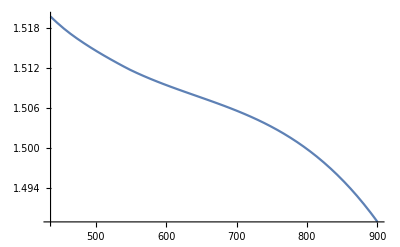

```mathematica
nCor = Import[materialdata[[4]],"Data"] ;(*4 Corning m*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nCor  = Drop[nCor,1];

nCorFunc=Interpolation[nCor/.{λ_,n_}-> { λ*1000,n}];
Plot[nCorFunc[λ],{λ,436,900}]
```

## H2O G. M. Hale and M. R. Querry. Optical constants of water in the 200-nm to 200-µm wavelength region, Appl. Opt. 12, 555-563 (1973)

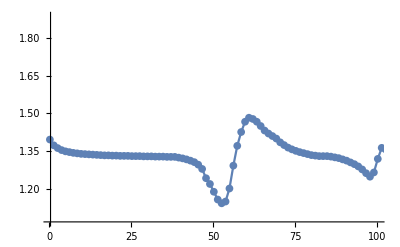
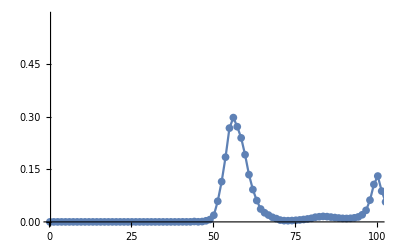

InterpolatingFunction[…]

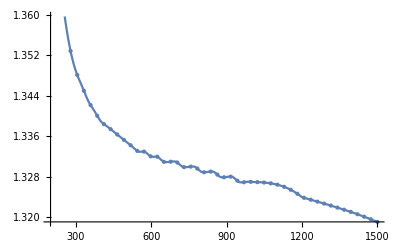

```mathematica
nH2O= Import[materialdata[[5]],"Data"] ;(*4 Corning m*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nH2O = Drop[nH2O,1];
ListLinePlot[nH2O[[;;,#]],Mesh->All,DataRange->nH2O[[{1,-1},1]],PlotRange->{{.4,100},{Automatic,Automatic}}]&/@{2,3}

nH2OFunc = Interpolation[nH2O/.{λ_,n_,κ_}-> {λ*1000,n}]
Plot[nH2OFunc[λ],{λ,200,1500},Mesh->Full]
```

## BK7 SCHOTT

InterpolatingFunction[…]

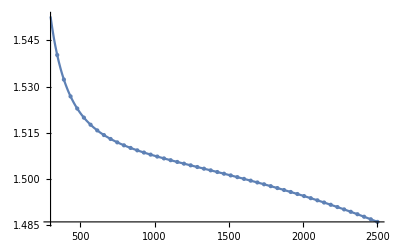

```mathematica
nBK7= Import[materialdata[[3]],"Data"] ;(*4 Corning m*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nBK7 = Drop[nBK7,1];

nBK7Func = Interpolation[nBK7[[;;,{1,2}]]]
Plot[nBK7Func[λ],{λ,300,2500},Mesh->Full]
```

## Si: Creo que es Aspens

```mathematica
nSieV = Import[materialdata[[6]],"Data"] ;(*1 es Ag, 2 es Au, 3 es en H2O en nm y 4 es en μm*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nSieV  = Drop[nSieV,1];

nSiFunc=Interpolation[nSieV/.{eV_,n_, κ_}-> { hc /eV,n+I κ}];
```

```mathematica
.
```

# Theory

### Fresnel

```mathematica
rs[θ_,ni_,nt_]:= With[{ n = nt/ni},(Cos[θ] -Sqrt[ n^2 - Sin[θ]^2] )/ ( Cos[θ] +Sqrt[ n^2- Sin[θ]^2])] 
rp[θ_,ni_,nt_]:= With[{ n = nt/ni},(n^2  * Cos[θ] - Sqrt[ n^2-Sin[θ]^2])/(n^2 * Cos[θ] + Sqrt[ n^2-Sin[θ]^2])  ]

ts[θ_,ni_,nt_]:= With[{ n = nt/ni},(2* Cos[θ]) / ( Cos[θ] +Sqrt[ n^2- Sin[θ]^2])] 
tp[θ_,ni_,nt_]:= With[{ n = nt/ni},(2*n  * Cos[θ] )/(n^2 * Cos[θ] + Sqrt[ n^2-Sin[θ]^2])  ]
```

```mathematica
brewA[ni_,nt_]:=ArcTan[nt/ni]
critA[ni_,nt_]:=ArcSin[nt/ni]
```

### Mie coefficients / π_n & τ_n

```mathematica
rbψ[n_,z_]:= z *SphericalBesselJ[n,z];
rbξ[n_,z_]:= z *SphericalHankelH1[n,z]
drbψ[n_,z_]:=-n *SphericalBesselJ[n,z]+ z * SphericalBesselJ[n-1,z]  
drbξ[n_,z_]:=-n * SphericalHankelH1[n,z] + z* SphericalHankelH1[n-1,z]
```

```mathematica
mieCoef2[n_,x_,m_]:= Module[{an,bn,ψnmx,dψnmx,ξnm,dξnm,ψnx,dψnx },  (*n=orden, x=size parameter, m = Subscript[n, part]/Subscript[n, medium]; si n es una lista -> {{Subscript[a, 1], Subscript[a, 2],...,Subscript[a, n]},{Subscript[b, 1], Subscript[b, 2],...,Subscript[b, n]}}, si no, sólo da la pareja*)

{ψnmx ,dψnmx}  = {m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]}&@ SphericalBesselJ[n,m*x];
{ψnx,dψnx }  = {x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@ SphericalBesselJ[n,x];
{ξnm,dξnm} = {ψnx,dψnx } + I*{x*#,-n*#+x*SphericalBesselY[n-1,x]}&@ SphericalBesselY[n,x];

an=(m *ψnmx*dψnx -  ψnx*dψnmx)/(m *ψnmx*dξnm-ξnm*dψnmx);
bn=(ψnmx*dψnx -m * ψnx*dψnmx)/(ψnmx*dξnm-m*ξnm*dψnmx);
{an,bn}]
```

```mathematica
mieCoef[n_,x_,m_]:= Module[{an,bn,ψdψ1,ψdψ2,ψdξ,ξdψ},  (*n=orden, x=size parameter, m = Subscript[n, part]/Subscript[n, medium]; si n es una lista -> {{Subscript[a, 1], Subscript[a, 2],...,Subscript[a, n]},{Subscript[b, 1], Subscript[b, 2],...,Subscript[b, n]}}, si no, sólo da la pareja*)
ψdψ1 = rbψ[n,m *x]*drbψ[n,x];
ψdψ2 = rbψ[n,x]*drbψ[n,m*x];
ψdξ = rbψ[n,m*x]*drbξ[n,x];
ξdψ = rbξ[n,x]*drbψ[n,m*x];

an=(m *ψdψ1 - ψdψ2)/(m *ψdξ-ξdψ);
bn=(ψdψ1 -m *ψdψ2)/(ψdξ-m*ξdψ);
{an,bn}]
```

```mathematica
pi[n_,θ_]:=Module[{f}, f[0]=0;f[1]=1;   f[i_]:=f[i]=(2 i -1)/(i-1)Cos[θ]f[i-1]-i/(i-1)f[i-2];f[n]]
tau[n_,θ_]:=Module[{f}, f[0]=0; f[1]=1; f[i_]:=f[i]=(2 i -1)/(i-1)Cos[θ]f[i-1]-i/(i-1)f[i-2]; n Cos[θ] f[n] - (n+1)f[n-1]]
```

```mathematica
scaQ[indices_,λ_,rad_]:= Module[{an,bn,sum, nmax,x},
x = 2* π *indices[[1]] *rad / λ;
{an,bn} = mieCoef[Table[i,{i,Round[x+4 x^(1/3)+2]}],x,indices[[2]]/indices[[1]]];
sum = Sum[(2*i+1)* (Abs[an[[i]] ]^2+Abs[bn[[i]] ]^2),{i, Length[an]}];
sum = ((λ^2 )* sum)/(2*π*( Abs[indices[[1]]]^2));
sum = sum / (π  *(rad^2))]

scaQ2[indices_,λ_,rad_]:= Module[{an,bn,sum, nmax,x},
x = 2* π *indices[[1]] *rad / λ;
{an,bn} = mieCoef2[Table[i,{i,Round[x+4 x^(1/3)+2]}],x,indices[[2]]/indices[[1]]];
sum = Sum[(2*i+1)* (Abs[an[[i]] ]^2+Abs[bn[[i]] ]^2),{i, Length[an]}];
sum = ((λ^2 )* sum)/(2*π*( Abs[indices[[1]]]^2));
sum = sum / (π  *(rad^2))]
```

```mathematica
extQ[indices_,λ_,rad_]:= Module[{sum,an,bn,nmax,x},
x = 2* π *indices[[1]] *rad / λ;
{an,bn} = mieCoef[Table[i,{i,Round[x+4 x^(1/3)+2]}],x,indices[[2]]/indices[[1]]];
sum = Sum[(2*i+1)* Re[ an[[i]] + bn[[i]]  ],{i, Length[an]}];
sum = ((λ^2 )* sum)/(2*π*( Abs[indices[[1]]]^2));
sum = sum / (π  *(rad^2))]

extQ2[indices_,λ_,rad_]:= Module[{sum,an,bn,nmax,x},
x = 2* π *indices[[1]] *rad / λ;
{an,bn} = mieCoef2[Table[i,{i,Round[x+4 x^(1/3)+2]}],x,indices[[2]]/indices[[1]]];
sum = Sum[(2*i+1)* Re[ an[[i]] + bn[[i]]  ],{i, Length[an]}];
sum = ((λ^2 )* sum)/(2*π*( Abs[indices[[1]]]^2));
sum = sum / (π  *(rad^2))]
```

# Gold NP

## Biosensor 12.5 Au NP@Air

```mathematica
FileNames["*.csv","Biosensor"]
data= Drop[Import[#,"Data"],5]&/@%;
```

{Biosensor/Eficiencias.csv,Biosensor/EficienciasSizeCorrection.csv,Biosensor/Eficiencias_SustratoVariableSystemDimensions.csv,Biosensor/Eficiencias_SusttratoFixedSystemDimensions.csv}

```mathematica
nAuSize[λ_,a_]:=Sqrt[εAuFuncSpline[λ]-(1-λ/λp^2*1/(1/λ + I/γ))+(1-λ/λp^2*1/(1/λ + I(1/γ+1/γsize)))/.{λp->142.609,γ->14966.2,γsize->(a *2 π c)/(1.4*^15)}(*Values for Au*)]

{sca,ext} = Transpose[Table[Through[{scaQ,extQ}[{1.,nAuFunc[λ]},λ,12.5]],{λ, 400,800}]];
{scaSize,extSize} = Transpose[Table[Through[{scaQ,extQ}[{1.,nAuSize[λ,12.5]},λ,12.5]],{λ, 400,800}]];
```

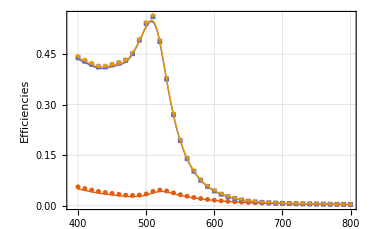

Biosensor/Mie_12-5nmAu_Air.pdf

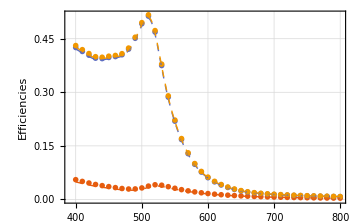

Biosensor/Mie_12-5nmAuSize_Air.pdf

-Graphics-

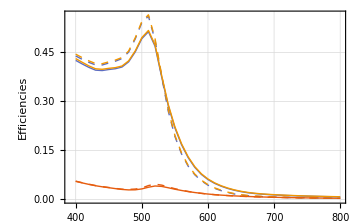

Biosensor/Mie_12-5nmAu(No)Size_Air.pdf

```mathematica
amp = 10;
Show[{ListPlot[If[#==3,data[[1,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[1,;;,{2,#}]]]&/@{3,4,5},PlotStyle->Thick,GridLines-> Automatic,PlotTheme->"Scientific",
Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},
PlotMarkers->{Automatic,5},
PlotLegends->Placed[MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],{Right,Top}]
,ImageSize-> Medium],
ListLinePlot[{sca*amp,ext-sca,ext},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"]}]
Export[FileNameJoin[{"Biosensor","Mie_12-5nmAu_Air.pdf"}],%]

Show[{ListPlot[If[#==3,data[[2,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[2,;;,{2,#}]]]&/@{3,4,5},PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> Automatic,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
PlotLegends->Placed[MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],{Right,Top}]
,ImageSize-> Medium],
ListLinePlot[{scaSize*amp,extSize-scaSize,extSize},DataRange->{400,800},PlotStyle->Directive[Thick,Dashed],PlotTheme-> "Scientific"]}]
Export[FileNameJoin[{"Biosensor","Mie_12-5nmAuSize_Air.pdf"}],%]

Show[{
Show[{ListPlot[If[#==3,data[[1,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[1,;;,{2,#}]]]&/@{3,4,5},PlotStyle->Thick,GridLines-> Automatic,PlotTheme->"Scientific",
Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{Automatic,5},
PlotLegends->Placed[MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],{Right,Top}]
,ImageSize-> Medium],
ListLinePlot[{sca*amp,ext-sca,ext},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"]}]
,
Show[{ListPlot[If[#==3,data[[2,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[2,;;,{2,#}]]]&/@{3,4,5},PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> Automatic,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5}
,ImageSize-> Medium],
ListLinePlot[{scaSize*amp,extSize-scaSize,extSize},DataRange->{400,800},PlotStyle->Directive[Thick,Dashed],PlotTheme-> "Scientific",
PlotLegends->Placed[LineLegend[{Black,Directive[Black,Dashed]},Style[#,texStyle]&/@{"No Size Correction", "Size Correction"},LegendLabel->Style["Mie Analytic Solution",texStyle]],{Right,Top}]
]}]
}]


Show[{ListLinePlot[If[#==3,data[[1,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[1,;;,{2,#}]]]&/@{3,4,5},PlotStyle->Directive[Dashed,Thick],GridLines-> Automatic,PlotTheme->"Scientific",
Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},
PlotLegends->Placed[MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],{Right,Top}]
,ImageSize-> Medium],
ListLinePlot[If[#==3,data[[2,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[2,;;,{2,#}]]]&/@{3,4,5},PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> Automatic,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"}
,ImageSize-> Medium]
}]
Export[FileNameJoin[{"Biosensor","Mie_12-5nmAu(No)Size_Air.pdf"}],%]
```

```mathematica
amp = 5
Show[{ListLinePlot[If[#==4,data[[4,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[4,;;,{2,#}]]]&/@{4,3,5},PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> Automatic,Mesh->None,
Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},
PlotLegends->Placed[MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],{Right,Top}]
,ImageSize-> Medium],
ListLinePlot[If[#==4,data[[3,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[3,;;,{2,#}]]]&/@{4,3,5},PlotStyle->Directive[Thick,Dashed],PlotTheme-> "Scientific",Mesh->None,
PlotLegends->Placed[LineLegend[{Black,Directive[Black,Dashed]},Style[#,texStyle]&/@{"Fixed System Size", "λ-Dependent System Size"}],{Right,Top}]
]}]
Export[FileNameJoin[{"Biosensor","12-5nmAu_Air_BK7.pdf"}],%]
```

5

-Graphics-

Biosensor/12-5nmAu_Air_BK7.pdf

```mathematica
amp = 5
Show[{ListLinePlot[{sca*amp,ext-sca,ext},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific",
GridLines-> Automatic,Mesh->None,
Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},
PlotLegends->Placed[MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],{Right,Top}]
,ImageSize-> Medium],
ListLinePlot[If[#==4,data[[3,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[3,;;,{2,#}]]]&/@{4,3,5},PlotStyle->Directive[Thick,Dashed],PlotTheme->"Scientific",
PlotLegends->Placed[LineLegend[{Directive[Black,Dashed],Black},Style[#,texStyle]&/@{"12.5nm-NP@Air/BK7 - COMSOL", "12.5nm-NP@Air - Mie"}],{Right,Top}]
]}]
Export[FileNameJoin[{"Biosensor","12-5nmAu_Air_BK7_Comp.pdf"}],%]
```

5

-Graphics-

Biosensor/12-5nmAu_Air_BK7_Comp.pdf

## Mie Dipole 5nm Au NP@Air

```mathematica
FileNames["*.csv","MieComsol"];
data= Drop[Import[#,"Data"],5]&/@%;
TableForm[%%]
```

MieComsol/1-IsolatedNP_crossSections-FEM.csv
MieComsol/2-mesh_pmlVariation.csv
MieComsol/3-mesh_NPVariation.csv
MieComsol/4-mesh_MAtrixVariation.csv
MieComsol/5-SupportedNP_crossSections-NormalIncidence_FEM.csv
MieComsol/nAu_5nm.csv
MieComsol/SupportedNP_crossSections-NormalIncidence_FEM.csv

```mathematica
nAuSize[λ_,a_]:=Sqrt[εAuFuncSpline[λ]-(1-λ/λp^2*1/(1/λ + I/γ))+(1-λ/λp^2*1/(1/λ + I(1/γ+1/γsize)))/.{λp->142.609,γ->14966.2,γsize->(a *2 π c)/(1.4*^15)}(*Values for Au*)]

{sca,ext} = Transpose[Table[Through[{scaQ,extQ}[{1.,nAuFunc[λ]},λ,5]],{λ, 400,800}]];
{scaSize,extSize} = Transpose[Table[Through[{scaQ,extQ}[{1.,nAuSize[λ,5]},λ,5]],{λ, 400,800}]];
```

```mathematica
AbsoluteTiming[{sca,ext} = Transpose[Table[Through[{scaQ,extQ}[{1.,nAuFunc[λ]},λ,5]],{λ, 400,800}]];]
AbsoluteTiming[{sca2,ext2} = Transpose[Table[Through[{scaQ2,extQ2}[{1.,nAuFunc[λ]},λ,5]],{λ, 400,800}]];]
```

{0.988073,Null}

{0.403868,Null}

```mathematica
Export["nAu_5nm.csv",Table[Flatten[{λ,ReIm[nAuSize[λ,5]]}],{λ,300,900}]]
```

nAu_5nm.csv

1000

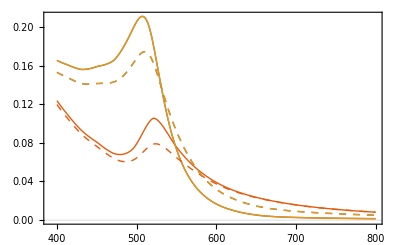

```mathematica
amp=1000
Show[{ListLinePlot[{sca*amp,ext-sca,ext},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"],
ListLinePlot[{scaSize*amp,extSize-scaSize,extSize},DataRange->{400,800},PlotStyle->Directive[Thick,Dashed],PlotTheme-> "Scientific"]}]
```

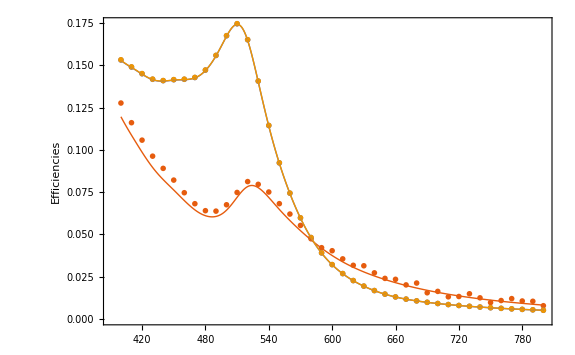

MieComsol/Mie-FEM.pdf

```mathematica
ii = 1;
amp = 1000;
(*sca, abs, ext*)
order = {3,4,5};
scadata  = 3;

Show[{ListPlot[If[#==scadata,data[[ii,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[ii,;;,{2,#}]]]&/@order,PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
PlotLegends->Placed[SwatchLegend[Automatic,MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],LegendLayout->"Row",
				LegendLabel->LineLegend[{Black,Black},Style[#,texStyle]&/@{"Mie","FEM"},LegendLayout->"Row",LegendMarkers->{None,Graphics[Circle[]]},
						LegendLabel->Style["5 nm-AuNP@Air\nNP Max Mesh Size -> radius/10\nPML Thickness -> λ/4\nMatrix Max Mesh Size -> λ/8",texStyle]
						]],{Right,Top}]
,ImageSize-> 400],
ListLinePlot[{scaSize*amp,extSize-scaSize,extSize},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"]}]
Export[FileNameJoin[{"MieComsol","Mie-FEM.pdf"}],%]
```

```mathematica
grMax[extQ[{1.,nAuSize[#,5]},#,5]&,{500,520}]
grMax[scaQ[{1.,nAuSize[#,5]},#,5]&,{500,550}]
q510=extQ[{1.,nAuSize[#,5]},#,5]&@510
```

510.169

523.947

0.174343

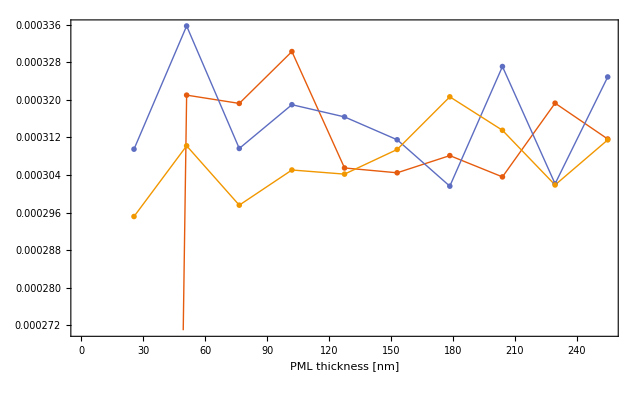

MieComsol/PML.pdf

```mathematica
ii = 2;
order = {5,4,3};
ListLinePlot[data[[ii,;;,{1,#}]]/.{x_,y_}-> {x,y-q510}&/@order,PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,Joined-> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{"PML thickness [nm]",MaTeX["Q_{ext}^{Mie} - Q_{ext}^{FEM}",FontSize->fs,ContentPadding->False]},PlotMarkers->{"OpenMarkers",5},
PlotLegends->Placed[LineLegend[Automatic,MaTeX[{"\\lambda/4","\\lambda/6","\\lambda/10"},ContentPadding->False],
LegendLabel->Style["5 nm-AuNP@Air; λ = 510 nm\nNP Max Mesh Size -> radius/3\nMatrix Max Mesh Size:",texStyle],LegendLayout->"Row"],{Right,Bottom}]
,ImageSize-> Medium,
FrameTicks->{{Automatic,Automatic},{Automatic,Table[{data[[ii,i,1]],MaTeX[λ*i/20]},{i,Length[data[[ii,;;,1]]]}]}}
]
Export[FileNameJoin[{"MieComsol","PML.pdf"}],%]
```

```mathematica
ii = 3;
order = {3};
Table[{1/(i),Abs[q510-data[[ii,i,3]]]},{i,Length[data[[ii,;;,3]]]}];
Table[{1/(i),Abs[q510-data[[ii,i,3]]]},{i,Length[data[[ii,;;,3]]]}];
Show[{ListLogLogPlot[%,Filling->Top,PlotStyle->Thick,PlotTheme->"Scientific",Frame->True,PlotRange->All,Joined->False,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{"Max Mesh Size of the NP [nm]",MaTeX["Q_{ext}^{FEM}-Q_{ext}^{Mie}",FontSize->fs,ContentPadding->False]},PlotMarkers->{"OpenMarkers",5}
,ImageSize-> 500,AspectRatio->1/3,
Epilog->{Inset[Style["5 nm-AuNP@Air; λ = 510 nm\nNP Matrix Mesh Size -> λ/6\nPML Thickness -> λ/4",texStyle],Scaled[{.8,.3}]]},
FrameTicks->{{Automatic,Automatic},{Table[{i,NumberForm[i*5,{2,1}]},{i,0.0,1,.2}],Table[{1/i,a/(i)},{i,Length[data[[ii,;;,3]]]}]}}
]},
Show[ListLogLogPlot[%,PlotTheme->"Scientific",Joined->True]]]
Export[FileNameJoin[{"MieComsol","radiusMesh.pdf"}],%]
```

```mathematica
ii = 4;
Table[{1/(2+i),Abs[q510-data[[ii,i,3]]]},{i,Length[data[[ii,;;,3]]]}];
Show[{ListLogLogPlot[%,Filling->Top,PlotStyle->Thick,PlotTheme->"Scientific",Frame->True,PlotRange->All,Joined->False,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{"Max Mesh Size of the Matrix [nm]",MaTeX["Q_{ext}^{FEM}-Q_{ext}^{Mie}",FontSize->fs,ContentPadding->False]},PlotMarkers->{"OpenMarkers",5}
,ImageSize-> 500,AspectRatio->1/3,
Epilog->{Inset[Style["5 nm-AuNP@Air; λ = 510 nm\nNP Max Mesh Size -> radius/10\nPML Thickness -> λ/4",texStyle],Scaled[{.8,.3}]]},
FrameTicks->{{Automatic,Automatic},{Table[{i,IntegerPart[i*510]},{i,0.0,.34,.03}],Table[{1/(2+i),λ/(i+2)},{i,Length[data[[ii,;;,3]]]}]}}
]},
Show[ListLogLogPlot[%,PlotTheme->"Scientific",Joined->True]]]
Export[FileNameJoin[{"MieComsol","MatrixMesh.pdf"}],%]
```

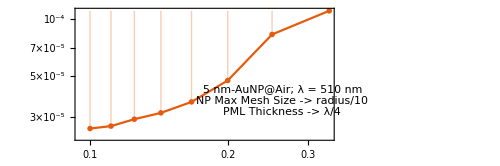

MieComsol/MatrixMesh.pdf

```mathematica
m=1-h/a
```

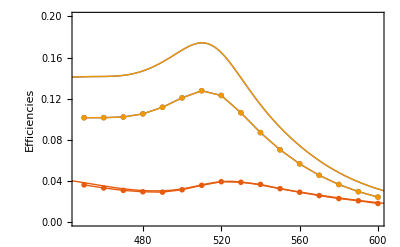

MieComsol/Supported-FEM.pdf

```mathematica
ii = 5;
amp = 500;
(*sca, abs, ext*)
order = {3,5,4};
scadata  = 3;

Show[{ListPlot[If[#==scadata,data[[ii,;;,{2,#}]]/.{x_,y_}-> {x,amp*y},data[[ii,;;,{2,#}]]]&/@order,PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,Joined-> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},PlotRange->.2,
PlotLegends->Placed[SwatchLegend[Automatic,MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],LegendLayout->"Column",
				LegendLabel->LineLegend[{Black,Black},Style[#,texStyle]&/@{"Isolated (Mie)","Supported BK7 (FEM)"},LegendLayout->"Column",LegendMarkers->{None,Graphics[Circle[]]},
						LegendLabel->Style["5 nm-AuNP@Air",texStyle]
						]],{Right,Top}]
,ImageSize-> 400],
ListLinePlot[{scaSize*amp,extSize-scaSize,extSize},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"]}]
Export[FileNameJoin[{"MieComsol","Supported-FEM.pdf"}],%]
```

## Supported NP

```mathematica
FileNames["*.csv","SupportedNP"];
data= Drop[Import[#,"Data"],5]&/@%;
TableForm[%%]
rad =12.5 (*nm*);
```

SupportedNP/12-5_Mie_Air.csv
SupportedNP/12-5_Mie_Bk7.csv
SupportedNP/12-5-SupportedNP_crossSections-NormalIncidence_all_FEM.csv
SupportedNP/AbsP_theta_c.csv
SupportedNP/AbsS_theta_c.csv
SupportedNP/dipolarApprox.csv
SupportedNP/nAu_12-5nm.csv
SupportedNP/ScaP_theta_c.csv
SupportedNP/ScaS_theta_c.csv

```mathematica
mieAir = data[[1,;;,{1,#}]]&/@{3,4,5};
miebk7=data[[2,;;,{1,#}]]&/@{3,4,5};

scaData = data[[3,;;,{1,#}]]&/@Range[3,Length[Transpose[data[[3]]]],3];
absData = data[[3,;;,{1,#}]]&/@Range[4,Length[Transpose[data[[3]]]],3];
extData = data[[3,;;,{1,#}]]&/@Range[5,Length[Transpose[data[[3]]]],3];

critP  = data[[4,;;,{2,#}]]&/@Range[3,Length[Transpose[data[[4]]]]];
critS = data[[5,;;,{2,#}]]&/@Range[3,Length[Transpose[data[[5]]]]];

dip = data[[6,;;,{1,#}]]&/@{2,4,6};
 critP= Partition[#,Length[critP]]&@Join[critP, data[[8,;;,{2,#}]]&/@Range[3,Length[Transpose[data[[8]]]]]];
critS = Partition[#,Length[critS]]&@Join[critS, data[[9,;;,{2,#}]]&/@Range[3,Length[Transpose[data[[9]]]]]];
```

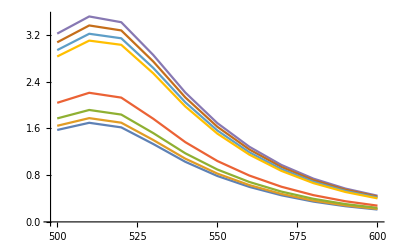
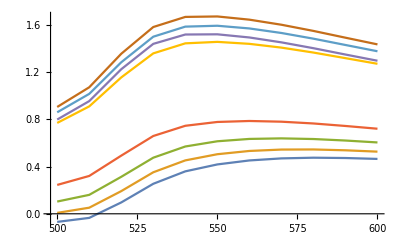

```mathematica
ListLinePlot/@critP
```

### Convergencia

```mathematica
nAuSize[λ_,a_]:=Sqrt[εAuFuncSpline[λ]-(1-λ/λp^2*1/(1/λ + I/γ))+(1-λ/λp^2*1/(1/λ + I(1/γ+1/γsize)))/.{λp->142.609,γ->14966.2,γsize->(a *2 π c)/(1.4*^15)}(*Values for Au*)]
Export[FileNameJoin[{"SupportedNP","nAu_12-5nm.csv"}],Table[Flatten[{λ,ReIm[nAuSize[λ,rad]]}],{λ,300,900}]]
```

SupportedNP/nAu_12-5nm.csv

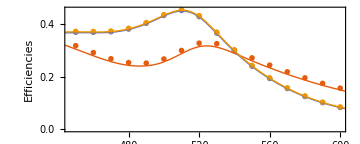

SupportedNP/Mie-FEM_Air.pdf

```mathematica
amp =100;
(*sca, abs, ext*)
order = {1,2,3};
scadata  = 1;

{scaSize,extSize} = Transpose[Table[Through[{scaQ,extQ}[{1.,nAuSize[λ,5]},λ,rad]],{λ, 400,800}]];
Show[{ListPlot[If[#==scadata,mieAir[[#]]/.{x_,y_}-> {x,amp*y},mieAir[[#]]]&/@order,PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
PlotLegends->Placed[SwatchLegend[Automatic,MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],LegendLayout->"Row",
				LegendLabel->LineLegend[{Black,Black},Style[#,texStyle]&/@{"Mie","FEM"},LegendLayout->"Row",LegendMarkers->{None,Graphics[Circle[]]},
						LegendLabel->Style["12.5 nm-AuNP@Air",texStyle]
						]],{Left,Bottom}]
,ImageSize-> Medium,AspectRatio->1/2.5],
ListLinePlot[{scaSize*amp,extSize-scaSize,extSize},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"]}]
Export[FileNameJoin[{"SupportedNP","Mie-FEM_Air.pdf"}],%]
```

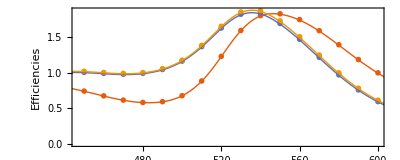

SupportedNP/Mie-FEM_BK7.pdf

```mathematica
amp =50;
(*sca, abs, ext*)
order = {1,2,3};
scadata  = 1;

{scaSize,extSize} = Transpose[Table[Through[{scaQ,extQ}[{1.5,nAuSize[λ,5]},λ,rad]],{λ, 400,800}]];
Show[{ListPlot[If[#==scadata,miebk7[[#]]/.{x_,y_}-> {x,amp*y/1.5},miebk7[[#]]/.{x_,y_}-> {x,y/1.5}]&/@order,PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
PlotLegends->Placed[SwatchLegend[Automatic,MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],LegendLayout->"Row",
				LegendLabel->LineLegend[{Black,Black},Style[#,texStyle]&/@{"Mie","FEM"},LegendLayout->"Row",LegendMarkers->{None,Graphics[Circle[]]},
						LegendLabel->Style["12.5 nm-AuNP@BK7",texStyle]
						]],{Right,Bottom}]
,ImageSize-> 400,AspectRatio->1/2.5],
ListLinePlot[{scaSize*amp,extSize-scaSize,extSize},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"]}]
Export[FileNameJoin[{"SupportedNP","Mie-FEM_BK7.pdf"}],%]
```

### IncrustedNP

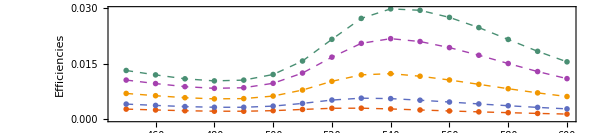
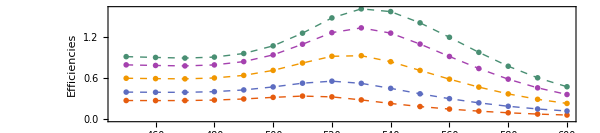
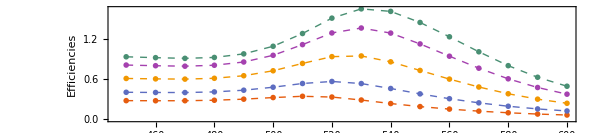

```mathematica
listFEM = ListLinePlot[#,PlotStyle->Directive[Thick,Dashed],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},PlotLegends->Placed[LineLegend[Automatic,Automatic,LegendLayout->"Row",
				LegendLabel->LineLegend[{Black,Black},Style[#,texStyle]&/@{"Mie","FEM"},LegendLayout->"Row",LegendMarkers->{None,Graphics[Circle[]]}
						]],{Right,Top}],
ImageSize-> 600,AspectRatio->1/4.5]&/@{scaData,absData,extData}
```

```mathematica
maximos = Table[{ref,grMax[extQ[{ref,nAuSize[#,5]},#,rad]&,{480,550}]},{ref,1,1.5,.01}];
maximosFH = maximos /.{n_,λ_}-> {n,λ,(n-1)/(1.5-1),1-2*(n-1)/(1.5-1)};
maximosFHeps = maximos /.{n_,λ_}-> {n,λ,(Sqrt[n]-1)/(Sqrt[1.5]-1),1-2*(Sqrt[n]-1)/(Sqrt[1.5]-1)};
```

```mathematica
neff = maximosFH[[;;,{-1,1}]]
nFunc = Interpolation[%]
nEpseff = maximosFHeps[[;;,{-1,1}]]
nFuncEps =Interpolation[%]
```

{{1.,1.},{0.96,1.01},{0.92,1.02},{0.88,1.03},{0.84,1.04},{0.8,1.05},{0.76,1.06},{0.72,1.07},{0.68,1.08},{0.64,1.09},{0.6,1.1},{0.56,1.11},{0.52,1.12},{0.48,1.13},{0.44,1.14},{0.4,1.15},{0.36,1.16},{0.32,1.17},{0.28,1.18},{0.24,1.19},{0.2,1.2},{0.16,1.21},{0.12,1.22},{0.08,1.23},{0.04,1.24},{0.,1.25},{-0.04,1.26},{-0.08,1.27},{-0.12,1.28},{-0.16,1.29},{-0.2,1.3},{-0.24,1.31},{-0.28,1.32},{-0.32,1.33},{-0.36,1.34},{-0.4,1.35},{-0.44,1.36},{-0.48,1.37},{-0.52,1.38},{-0.56,1.39},{-0.6,1.4},{-0.64,1.41},{-0.68,1.42},{-0.72,1.43},{-0.76,1.44},{-0.8,1.45},{-0.84,1.46},{-0.88,1.47},{-0.92,1.48},{-0.96,1.49},{-1.,1.5}}

InterpolatingFunction[…]

{{1.,1.},{0.955616,1.01},{0.911451,1.02},{0.867502,1.03},{0.823765,1.04},{0.780239,1.05},{0.736919,1.06},{0.693804,1.07},{0.650889,1.08},{0.608172,1.09},{0.565651,1.1},{0.523323,1.11},{0.481185,1.12},{0.439235,1.13},{0.397469,1.14},{0.355887,1.15},{0.314485,1.16},{0.273261,1.17},{0.232213,1.18},{0.191339,1.19},{0.150636,1.2},{0.110102,1.21},{0.0697354,1.22},{0.0295338,1.23},{-0.0105047,1.24},{-0.050382,1.25},{-0.0901002,1.26},{-0.129661,1.27},{-0.169066,1.28},{-0.208318,1.29},{-0.247418,1.3},{-0.286368,1.31},{-0.32517,1.32},{-0.363824,1.33},{-0.402334,1.34},{-0.4407,1.35},{-0.478925,1.36},{-0.517009,1.37},{-0.554954,1.38},{-0.592763,1.39},{-0.630435,1.4},{-0.667973,1.41},{-0.705378,1.42},{-0.742652,1.43},{-0.779796,1.44},{-0.816811,1.45},{-0.853698,1.46},{-0.89046,1.47},{-0.927096,1.48},{-0.963609,1.49},{-1.,1.5}}

InterpolatingFunction[…]

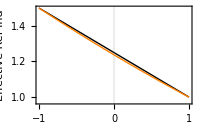

SupportedNP/fit.pdf

```mathematica
ListLinePlot[{neff,nEpseff},PlotStyle->{Directive[Thick,Black],Directive[Thick,Orange]},PlotTheme-> "Scientific",FrameStyle->Black,ImageSize->200,
FrameLabel->{Style["h/a",texStyle,Italic],Style["Effective Ref Ind",texStyle]},PlotLegends->Placed[MaTeX[{"n_{eff}^{\\text{Mie}}","\\varepsilon_{eff}^{\\text{Mie}}"}],{Right,Top}]]
Export[FileNameJoin[{"SupportedNP","fit.pdf"}],%]
```

```mathematica
Show[{ListLinePlot[%%,Mesh->Full,PlotTheme-> "Scientific",PlotStyle->Blue,FrameStyle->Black,ImageSize->200,
FrameLabel->{Style["Matrix Refractive index",texStyle],Style["λ - LSPR",texStyle]}
],Plot[lm[x],{x,1,1.5},PlotStyle->Red]}]
Export[FileNameJoin[{"SupportedNP","fit.pdf"}],%]

max = Max/@absData[[;;,;;,2]]
maxl = Table[Flatten@Select[absData[[i]],#[[2]]==max[[i]]&],{i,5}][[;;,1]]
refInd = Flatten[(x/.Solve[lm[x]==#,x]&/@maxl)]
```

```mathematica
refInd = Flatten[(x/.Solve[lm[x]==#,x]&/@{510,520,525,530,534.5})]
```

{1.00815,1.21003,1.31097,1.41191,1.50275}

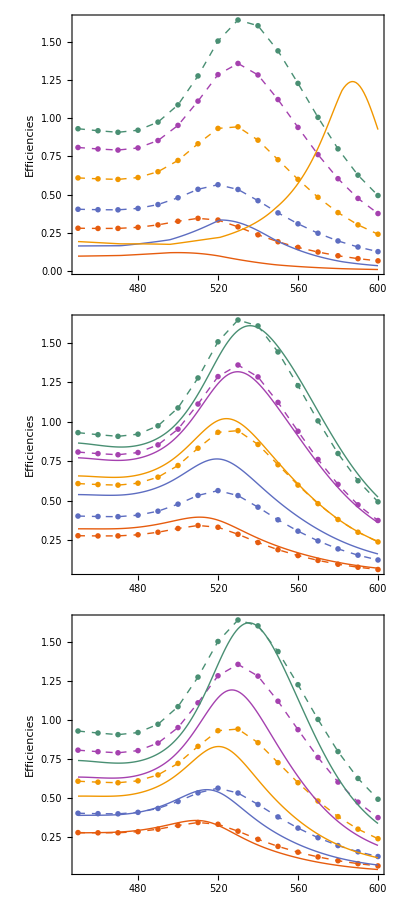

SupportedNP/Cases.pdf

```mathematica
ext = Table[
nAve = (1*(1-n)+1.5*n);
{λ,extQ[{nAve,nAuSize[λ,12.5]},λ,12.5]},{n,0,1,.25},{λ, 450,600}];
amp = .7;
extMie = ListLinePlot[ext/.{x_,y_}-> {x,amp*y},PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"}
,ImageSize->  600,AspectRatio->1/4.5];


amp =.85;
ext = Table[
{λ,extQ[{n,nAuSize[λ,5]},λ,12.5]},{n,refInd},{λ, 450,600}];
extMie2 = ListLinePlot[ext/.{x_,y_}-> {x,amp*y},PlotStyle->Directive[Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},
ImageSize->  600,AspectRatio->1/4.5];

dipplot= ListLinePlot[dip[[;;,47;;197,;;]],PlotStyle->Directive[Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotRange->Full,
ImageSize-> 600,AspectRatio->1/4.5];

Column[Map[Show[{listFEM[[3]],#},PlotRange-> All]&,{dipplot,extMie2,extMie}]]
Export[FileNameJoin[{"SupportedNP","Cases.pdf"}],%]
```

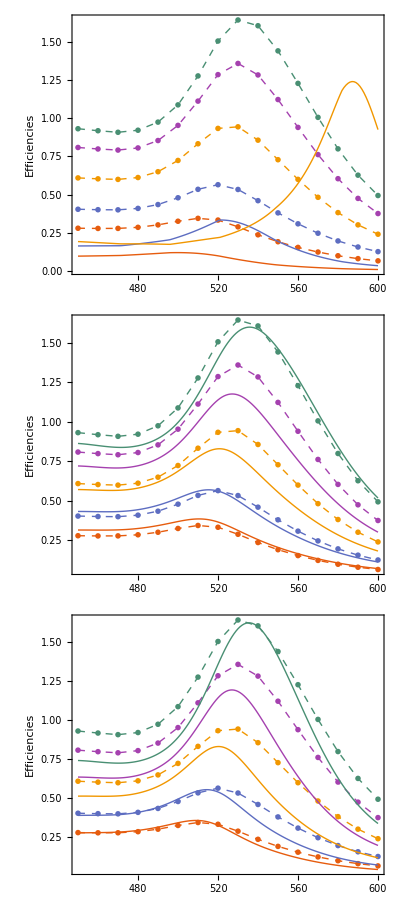

SupportedNP/CasesFit_1.pdf

```mathematica
ext = Table[
{λ,extQ[{nFunc[hh],nAuSize[λ,12.5]},λ,12.5]},{hh,1,-1,-.5},{λ, 450,600}];
amp = .7;
extMie = ListLinePlot[ext/.{x_,y_}-> {x,amp*y},PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"}
,ImageSize->  600,AspectRatio->1/4.5];

amp =.85;
ext = Table[
{λ,extQ[{nFuncEps[hh],nAuSize[λ,5]},λ,12.5]},{hh,1,-1,-.5},{λ, 450,600}];
extMie2 = ListLinePlot[ext/.{x_,y_}-> {x,amp*y},PlotStyle->Directive[Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},
ImageSize->  600,AspectRatio->1/4.5];

dipplot= ListLinePlot[dip[[;;,47;;197,;;]],PlotStyle->Directive[Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotRange->Full,
ImageSize-> 600,AspectRatio->1/4.5];

Column[Map[Show[{listFEM[[3]],#},PlotRange-> All]&,{dipplot,extMie2,extMie}]]
Export[FileNameJoin[{"SupportedNP","CasesFit_1.pdf"}],%]
```

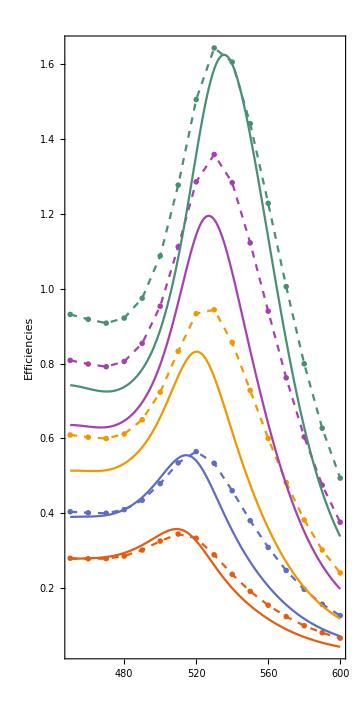
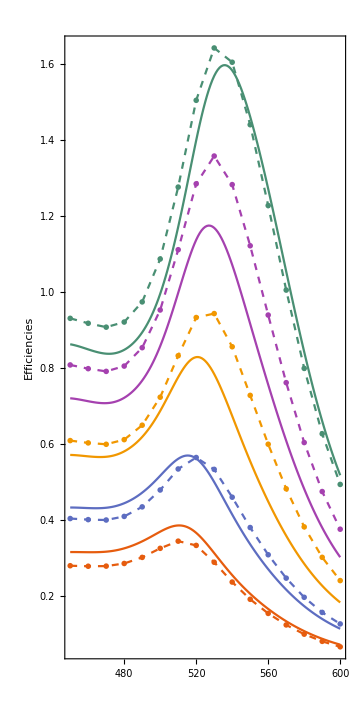
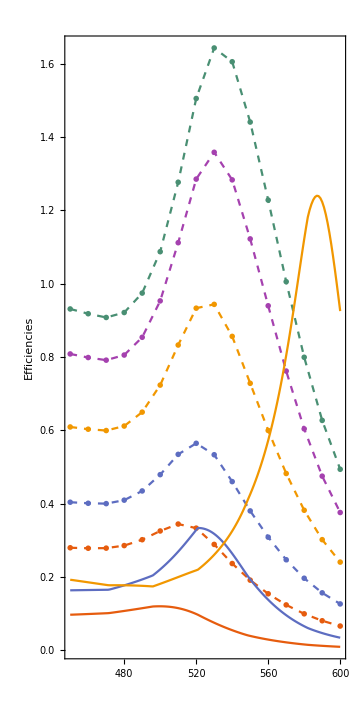

SupportedNP/CasesFit_2.pdf

```mathematica
Row[Map[Show[{listFEM[[3]],#},PlotRange-> All,AspectRatio-> 2,ImageSize-> Medium]&,{extMie,extMie2,dipplot}]]
Export[FileNameJoin[{"SupportedNP","CasesFit_2.pdf"}],%]
```

## Single Particle - Supported NP

```mathematica
FileNames["*.csv","Single particle_Supported",Infinity];
data= Drop[Import[#,"Data"],5]&/@%;
TableForm[%%]
rad =12.5 (*nm*);
```

Single particle_Supported/1-Abs-Sca_th_c/AbsS_theta_c.csv
Single particle_Supported/1-Abs-Sca_th_c/ScaS_theta_c.csv
Single particle_Supported/2-Abs-Sca_th_i/AbsP_theta_i.csv
Single particle_Supported/2-Abs-Sca_th_i/AbsS_theta_i.csv
Single particle_Supported/2-Abs-Sca_th_i/ScaP_theta_i.csv
Single particle_Supported/2-Abs-Sca_th_i/ScaS_theta_i.csv
Single particle_Supported/3-Far Field 2D/Efar_pPol_normalX_500nm.csv
Single particle_Supported/3-Far Field 2D/Efar_pPol_normalY_500nm.csv
Single particle_Supported/3-Far Field 2D/Efar_sPol_normalX_500nm.csv
Single particle_Supported/3-Far Field 2D/Efar_sPol_normalY_500nm.csv
Single particle_Supported/4-Normal incidence/Efar_pPol_theta_i0_normalX.csv
Single particle_Supported/4-Normal incidence/Efar_pPol_theta_i0_normalY.csv
Single particle_Supported/4-Normal incidence/Efar_sPol_theta_i0_normalX.csv
Single particle_Supported/4-Normal incidence/Efar_sPol_theta_i0_normalY.csv
Single particle_Supported/4-Normal incidence/Q_normalIncidence_p.csv
Single particle_Supported/4-Normal incidence/Q_normalIncidence_s.csv
Single particle_Supported/5-external_all.csv
Single particle_Supported/6-internal_all.csv

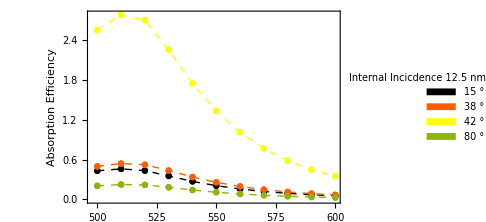
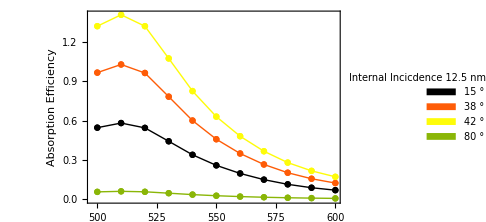

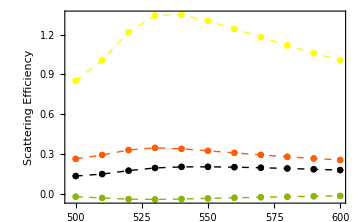
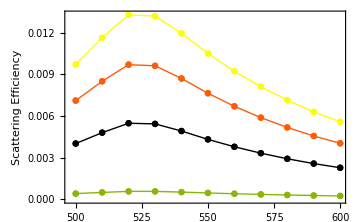

Single particle_Supported/Efficiencies_Angles.svg

```mathematica
absAngle=Transpose@(data[[3;;4,;;,{2,#}]]&/@Range[3,6]) (*absorption - 15, 38, 42, 80, P/S*);
scaAngle = Transpose@(data[[5;;6,;;,{2,#}]]&/@Range[3,6]) (*absorption - 15, 38, 42, 80, P/S*);

ListPlot[absAngle[[#]],Joined-> True,Mesh->Full,PlotRange->Full,
BaseStyle->texStyle,PlotStyle->Table[Directive[Thick,{Dashed,Thick}[[#]],ColorData[3,i]],{i,4}],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],Joined->True,Mesh->True,
FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Absorption Efficiency"},
ImageSize->Medium,
PlotLegends->Placed[SwatchLegend[Automatic,Style[#,texStyle]&/@{15,38,42,80}Degree,LegendLayout->"Row",
				LegendLabel->Style["Internal Incicdence\n12.5 nm-AuNP@Air/BK7",texStyle]
				],{Right,Top}]
]&/@Range[2]

ListPlot[scaAngle[[#]],Joined-> True,Mesh->Full,
BaseStyle->texStyle,PlotStyle->Table[Directive[Thick,{Dashed,Thick}[[#]],ColorData[3,i]],{i,4}],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],Joined->True,Mesh->True,
FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Scattering Efficiency"},
ImageSize->Medium]&/@Range[2]

Export[FileNameJoin[{"Single particle_Supported","Efficiencies_Angles.svg"}],Grid[{%%,%}]]
```

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,90-i,
i< 180,Mod[i,90],
i< 270,90-Mod[i,90],
True, Mod[i,90]
]Degree},{i,0,360,15}]
```

{{0.,90 °},{0.261799,75 °},{0.523599,60 °},{0.785398,45 °},{1.0472,30 °},{1.309,15 °},{1.5708,0},{1.8326,15 °},{2.0944,30 °},{2.35619,45 °},{2.61799,60 °},{2.87979,75 °},{3.14159,90 °},{3.40339,75 °},{3.66519,60 °},{3.92699,45 °},{4.18879,30 °},{4.45059,15 °},{4.71239,0},{4.97419,15 °},{5.23599,30 °},{5.49779,45 °},{5.75959,60 °},{6.02139,75 °},{6.28319,0}}

```mathematica
scatteredField = Partition[#,101]&/@(Drop[#,3]&/@data[[7;;10]]) ;
ListPolarPlot[scatteredField[[#]]/.{theta_,radius_}-> {theta+π/2,radius},BaseStyle->texStyle,Joined->True,Mesh->All,PlotStyle->Table[Directive[PointSize[Medium],ColorData[3,i]],{i,4}], PolarAxes->True,PlotRange->{2.25*^-7,3.5*^-7,1.5*^-9,1.5*^-9}[[#]],PlotTheme->"Grid",ImageSize->Medium,
PolarTicks->{thTiks,Automatic}
]&/@Range[4]
Export[FileNameJoin[{"Single particle_Supported","scattered_"<>ToString[#]<>".svg"}],%[[#]]]&/@Range[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{Single particle_Supported/scattered_1.svg,Single particle_Supported/scattered_2.svg,Single particle_Supported/scattered_3.svg,Single particle_Supported/scattered_4.svg}

```mathematica
scatteredFieldNormal = Partition[#,101]&/@(Drop[#,3]&/@data[[11;;14]]) ;
ListPolarPlot[#/.{theta_,radius_}-> {theta+π/2,radius},BaseStyle->texStyle,Joined->True,Mesh->All,PlotStyle->Table[Directive[PointSize[Medium],ColorData[3,i]],{i,Length[#]}], PolarAxes->True,PlotRange->11.5*^-10,PlotTheme->"Grid",ImageSize->Medium,
PolarTicks->{thTiks,Automatic}
]&/@scatteredFieldNormal
Export[FileNameJoin[{"Single particle_Supported","scattered_normal_"<>ToString[#]<>".svg"}],%[[#]]]&/@Range[4]
Export[FileNameJoin[{"Single particle_Supported","lambda_legends.svg"}],
			SwatchLegend[ColorData[3,#]&/@Range[11],Style[ToString[#]<>" nm",texStyle]&/@Range[500,600,10],LegendLayout->"Row",
				LegendLabel->Style["Normal Incidence\n12.5 nm-AuNP@Air/BK7",texStyle]]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{Single particle_Supported/scattered_normal_1.svg,Single particle_Supported/scattered_normal_2.svg,Single particle_Supported/scattered_normal_3.svg,Single particle_Supported/scattered_normal_4.svg}

Single particle_Supported/lambda_legends.svg

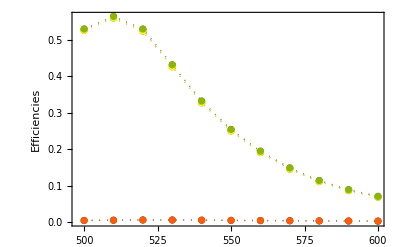

Single particle_Supported/Q_normal.svg

```mathematica
(*Normal incidence (p,s)*)
ListPlot[#,BaseStyle->texStyle,PlotStyle->Table[Directive[Thick,Dotted,ColorData[4,i]],{i,2,4}],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],Joined->True,Mesh->True,
FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"}
]&@(data[[15,;;,{2,#}]]&/@Range[3,5]);

ListPlot[#,BaseStyle->texStyle,PlotStyle->Table[Directive[Thick,Dotted,ColorData[3,i]],{i,2,4}],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],Joined->True,Mesh->True,
FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"}
]&@(data[[16,;;,{2,#}]]&/@Range[3,5]);

Show[{%%,%}]
Export[FileNameJoin[{"Single particle_Supported","Q_normal.svg"}],%]
```

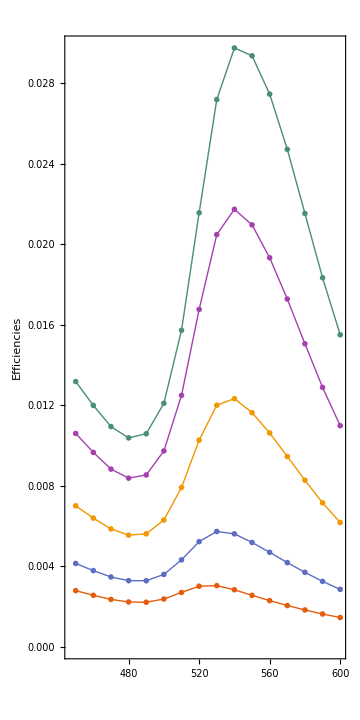
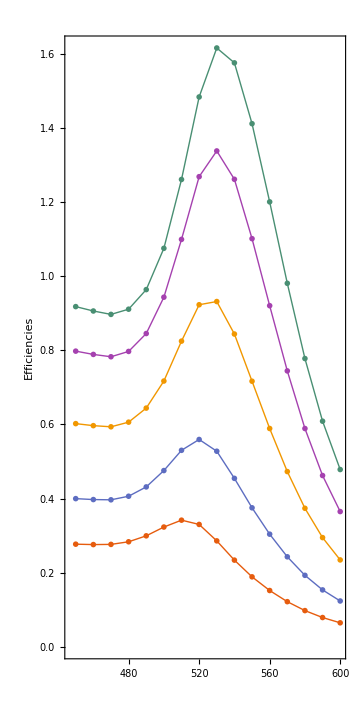
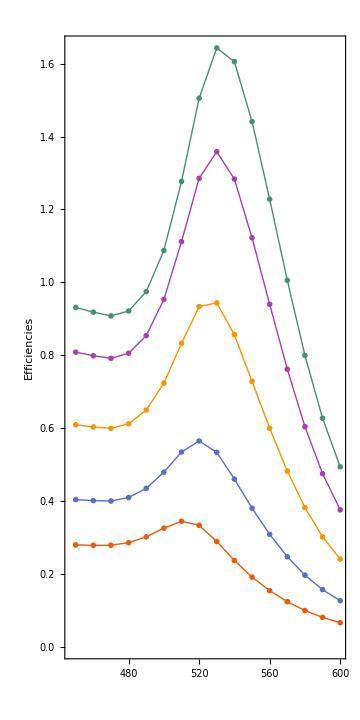

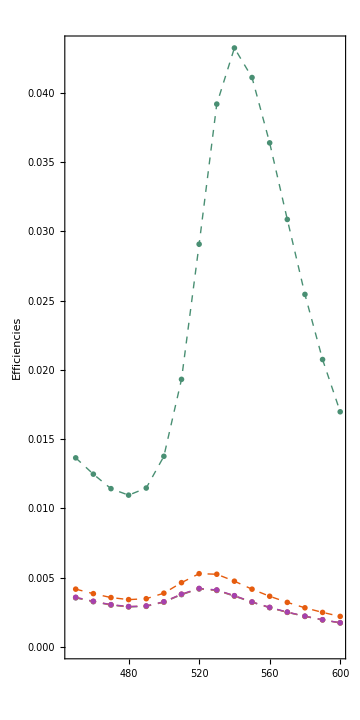
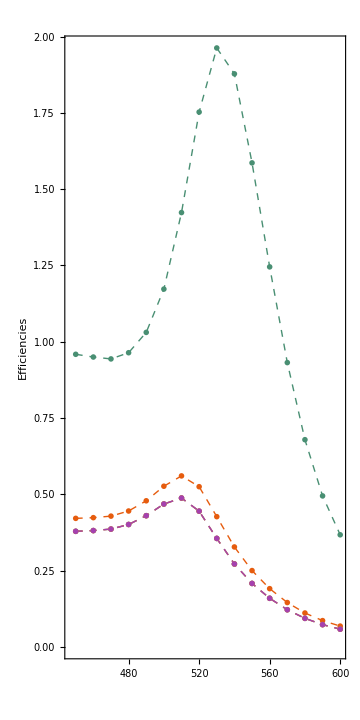
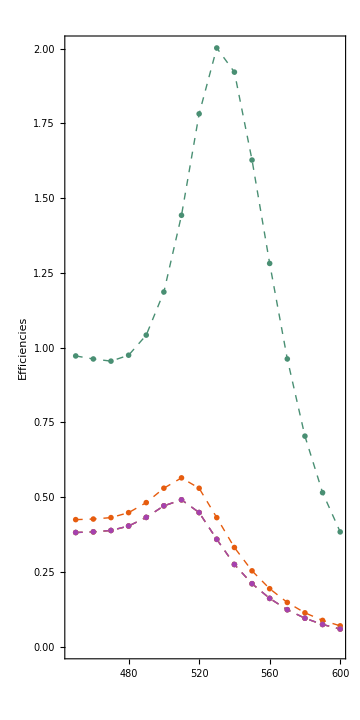

```mathematica
(*ListLinePlot[#,PlotStyle->Directive[Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->2]&/@ (data[[17,;;,{1,#}]]&/@Range[#,3*5+1,3]&/@Range[2,4])*)

ListLinePlot[#,PlotStyle->Directive[Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->2]&/@{scaData,absData,extData}
(*MapThread[Show,{%,%%}]*)


ListLinePlot[#,PlotStyle->Directive[Thick,Dashed],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->2,PlotRange->All]&/@ Reverse/@(data[[18,;;,{1,#}]]&/@Range[#,3*5+1,3]&/@Range[2,4])

(*Export[FileNameJoin[{"Single particle_Supported","Q_int_ext.svg"}],Row[%]]*)
```

## Incrusted Cases

```mathematica
FileNames[FileNameJoin[{"Incrusted","*.csv"}]]
data = Drop[ Import[#,"Data"],6]& /@%;
```

{Incrusted/IlluminatedAir.csv,Incrusted/IlluminatedBK7.csv}

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
```

#### Data

```mathematica
{fromAir,fromBK7} = Transpose@Table[{data[[2,;;,{1,#}]]& /@ Range[i,Length[data[[1,1]] ], 3],Reverse@(data[[1,;;,{1,#}]]& /@Range[i,Length[data[[1,1]] ], 3])},{i,2,4}];
```

```mathematica
nAuSize[λ_,a_]:=Sqrt[εAuFuncSpline[λ]-(1-λ/λp^2*1/(1/λ + I/γ))+(1-λ/λp^2*1/(1/λ + I(1/γ+1/γsize)))/.{λp->142.609,γ->14966.2,γsize->(a *2 π c)/(1.4*^15)}(*Values for Au*)]
sca = Table[{λ,scaQ[{1.,nAuSize[λ,12.5]},λ,12.5],scaQ[{1.5,nAuSize[λ,12.5]},λ,12.5]},{λ, 450,600}];
sca = Transpose[sca /.{x_,y_,z_}-> {{x,y},{x,z}}];

ext = Table[{λ,extQ[{1.,nAuSize[λ,12.5]},λ,12.5],extQ[{1.5,nAuSize[λ,12.5]},λ,12.5]},{λ, 450,600}];
ext = Transpose[ext /.{x_,y_,z_}-> {{x,y},{x,z}}];

abs = Transpose[{ext[[1,;;,1]],#}]&/@( ext[[;;,;;,2]]-sca[[;;,;;,2]]);
```

#### Graphs Mie - Incrusted

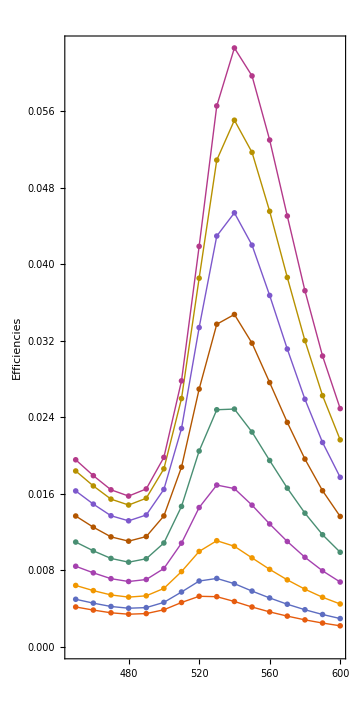
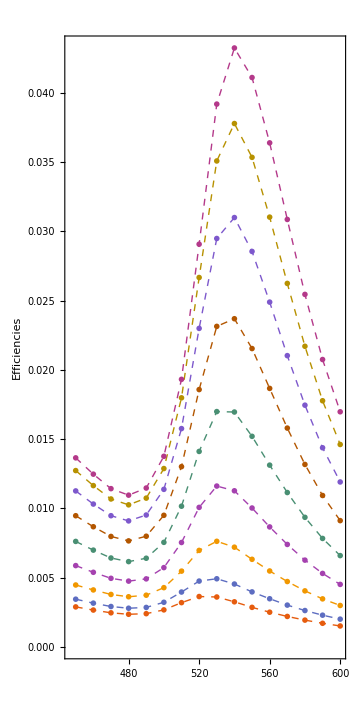
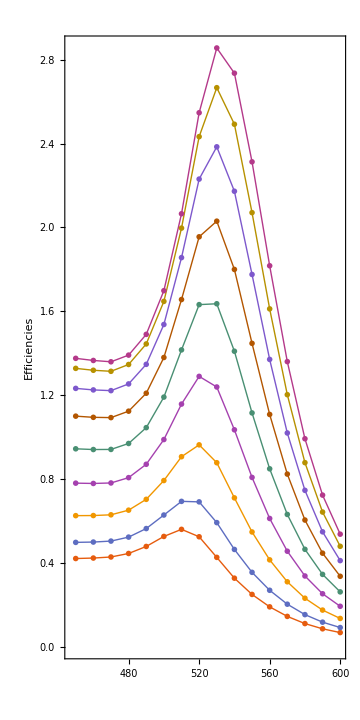
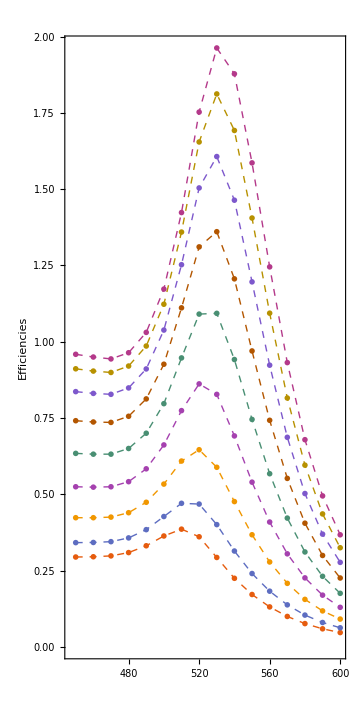
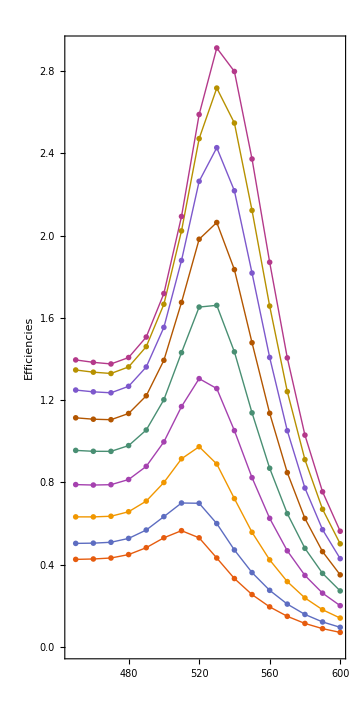
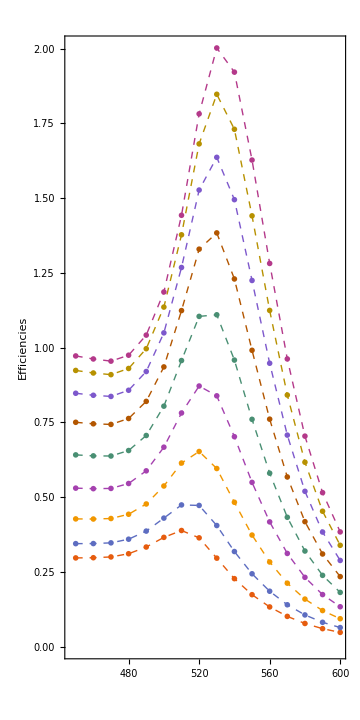

```mathematica
Table[{ListLinePlot[#,PlotStyle->Directive[Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->2]&@ (data[[2,;;,{1,#}]]& /@ Range[i,Length[data[[1,1]] ], 3])
,
ListLinePlot[#,PlotStyle->Directive[Thick,Dashed],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->2,PlotRange->All]&@ Reverse@(data[[1,;;,{1,#}]]& /@Range[i,Length[data[[1,1]] ], 3])
},{i,2,4}];
```

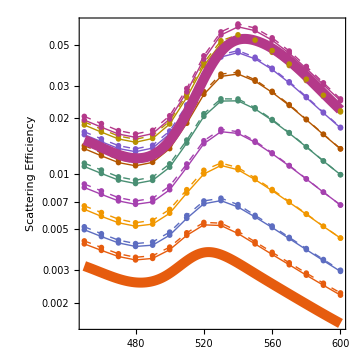
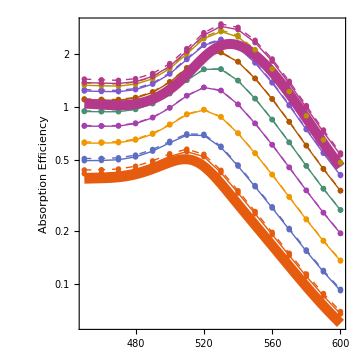
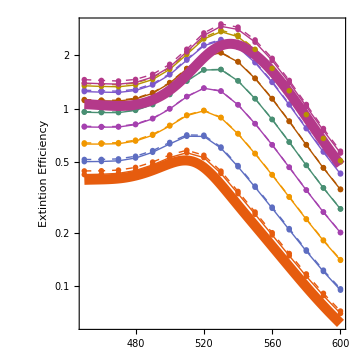

```mathematica
label = #<>"Efficiency"&/@{"Scattering ", "Absorption ", "Extintion "};
algo = Array[{ListLogPlot[fromAir[[#1,#2]]/.{x_,y_}-> {x,1.*y},PlotStyle->Directive[colors[[#2]],Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True, Joined -> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],label[[#1]]},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->1],
ListLogPlot[fromBK7[[#1,#2]]/.{x_,y_}-> {x,1.5*y},PlotStyle->Directive[colors[[#2]],Thick,Dashed],PlotTheme->"Scientific",GridLines-> None,Frame->True,Joined -> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],label[[#1]]},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->1,PlotRange->All]}
&,{3,9}];

mie = ListLogPlot[#,Joined -> True,PlotStyle->(Directive[Thickness[.02],#]&/@colors[[{1,9}]])]&/@{sca,abs,ext};

logPlots = Show[Append[algo[[#]],mie[[#]]],PlotRange-> All]&/@Range[3]
(*Export[FileNameJoin[{"Incrusted","logPlot_"<>ToString[#]<>".svg"}],logPlots[[#]]]&/@Range[3]*)
```

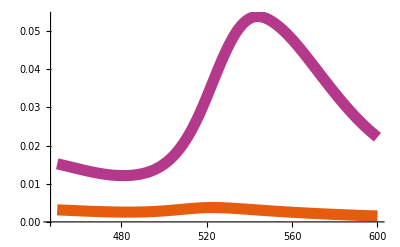
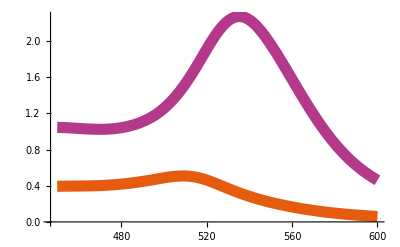
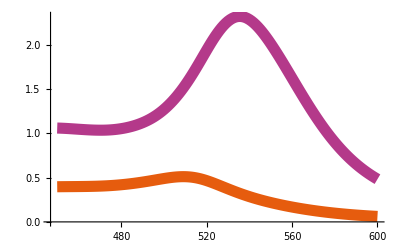

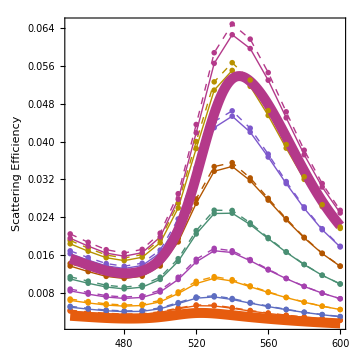
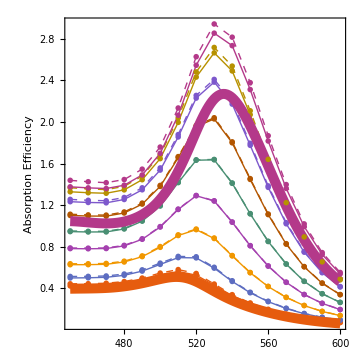
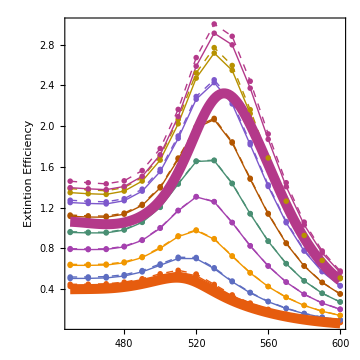

```mathematica
label = #<>"Efficiency"&/@{"Scattering ", "Absorption ", "Extintion "};
algo = Array[{ListPlot[fromAir[[#1,#2]]/.{x_,y_}-> {x,1.*y},PlotStyle->Directive[colors[[#2]],Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True, Joined -> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],label[[#1]]},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->1],
ListPlot[fromBK7[[#1,#2]]/.{x_,y_}-> {x,1.5*y},PlotStyle->Directive[colors[[#2]],Thick,Dashed],PlotTheme->"Scientific",GridLines-> None,Frame->True,Joined -> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],label[[#1]]},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->1,PlotRange->All]}
&,{3,9}];

mie = ListPlot[#,Joined -> True,PlotStyle->(Directive[Thickness[.02],#]&/@colors[[{1,9}]])]&/@{sca,abs,ext}

regularPlots = Show[Append[algo[[#]],mie[[#]]],PlotRange-> All]&/@Range[3]

(*Export[FileNameJoin[{"Incrusted","regPlot_"<>ToString[#]<>".svg"}],regularPlots[[#]]]&/@Range[3]*)
```

```mathematica
Export[FileNameJoin[{"Incrusted","plots.svg"}],Grid[{regularPlots,logPlots}]]
```

Incrusted/plots.svg

#### Graphs Effective Ref index

```mathematica
maximos = Table[{ref,grMax[extQ[{ref,nAuSize[#,12.5]},#,12.5]&,{480,550}]},{ref,1,1.5,.01}];
mExt = maximos /.{n_,λ_}-> {n,λ,(Sqrt[n]-1)/(Sqrt[1.5]-1),1-2*(Sqrt[n]-1)/(Sqrt[1.5]-1)};

maximos= Table[{ref,grMax[scaQ[{ref,nAuSize[#,12.5]},#,12.5]&,{480,550}]},{ref,1,1.5,.01}];
mSca = maximos /.{n_,λ_}-> {n,λ,(Sqrt[n]-1)/(Sqrt[1.5]-1),1-2*(Sqrt[n]-1)/(Sqrt[1.5]-1)};

nExt = mExt[[;;,{-1,1}]];
nExtFunc =Interpolation[%]
λExt = mExt[[;;,{-1,2}]];
λExtFunc = Interpolation[%]

nSca= mSca[[;;,{-1,1}]];
nScaFunc=Interpolation[%]
λSca = mSca[[;;,{-1,2}]];
λScaFunc = Interpolation[%]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

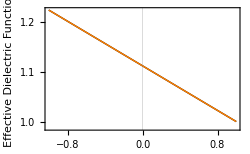

Incrusted/fit.svg

```mathematica
fitPlot  = ListLinePlot[{nSca/.{x_,y_}-> {x,Sqrt[y]},nExt/.{x_,y_}-> {x,Sqrt[y]}},PlotStyle->{Directive[Thick,Black],Directive[Thick,Orange]},PlotTheme-> "Scientific",FrameStyle->Black,ImageSize->250,
FrameLabel->{Style["h/a",texStyle,Italic],Style["Effective Dielectric Function",texStyle]},PlotLegends->Placed[
LineLegend[Automatic,Style[#,texStyle]&/@{"Scattering","Extintion"},LegendLabel->MaTeX["\\varepsilon_{eff}^{\\text{Mie}}"]],{Right,Top}]]
Export[FileNameJoin[{"Incrusted","fit.svg"}],%]
```

```mathematica
(*sca = Table[{λ,scaQ[{nScaFunc[ha],nAuSize[λ,12.5]},λ,12.5]},{ha,1,-1,-.25},{λ, 450,600}];
ext = Table[{λ,extQ[{nScaFunc[ha],nAuSize[λ,12.5]},λ,12.5]},{ha,1,-1,-.25},{λ, 450,600}];
abs = Transpose[{ext[[1,;;,1]],#}]&/@( ext[[;;,;;,2]]-sca[[;;,;;,2]]);
*)
sca = Table[{λ,scaQ[{nScaFunc[ha],nAuSize[λ,12.5]},λ,12.5]},{ha,1,-1,-.25},{λ, 450,600}];
ext = Table[{λ,extQ[{nScaFunc[ha],nAuSize[λ,12.5]},λ,12.5]},{ha,1,-1,-.25},{λ, 450,600}];
abs = Transpose[{ext[[1,;;,1]],#}]&/@( ext[[;;,;;,2]]-sca[[;;,;;,2]]);
```

{{{1.,524.135},{0.75,528.222},{0.5,530.546},{0.25,533.05},{0.,534.993},{-0.25,537.01},{-0.5,538.811},{-0.75,540.},{-1.,540.798}},{{1.,510.},{0.75,515.002},{0.5,520.},{0.25,522.161},{0.,525.419},{-0.25,528.022},{-0.5,530.},{-0.75,530.266},{-1.,531.966}}}

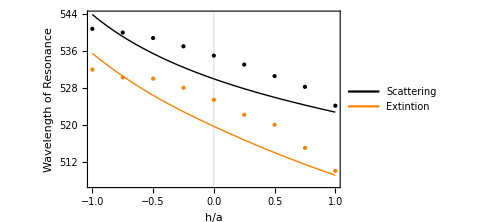

Incrusted/maxFit.svg

```mathematica
algo2 = Transpose@Table[
intS = Interpolation[fromAir[[1,i]]];
intE = Interpolation[fromAir[[3,i]]];
{{1.25-i*.25, grMax[intS,{480,550}]},{1.25-i*.25, grMax[intE,{480,550}]}},{i,9}]


Show[{ListLinePlot[{λSca,λExt},PlotStyle->{Directive[Thick,Black],Directive[Thick,Orange]},PlotTheme-> "Scientific",FrameStyle->Black,ImageSize->Medium,
FrameLabel->{Style["h/a",texStyle,Italic],Style["Wavelength of Resonance",texStyle]},PlotLegends->Placed[
LineLegend[Automatic,Style[#,texStyle]&/@{"Scattering","Extintion"}],{Left,Bottom}]],
ListPlot[algo2,PlotStyle->{Directive[Black,PointSize[Medium]],Directive[Orange,PointSize[Medium]]}]}]
Export[FileNameJoin[{"Incrusted","maxFit.svg"}],%]
```

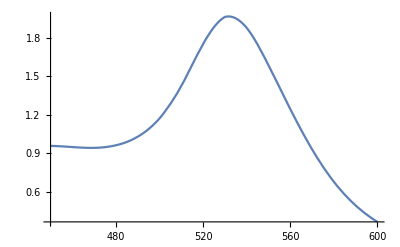

```mathematica
Plot[int[x],{x,450,600}]
```

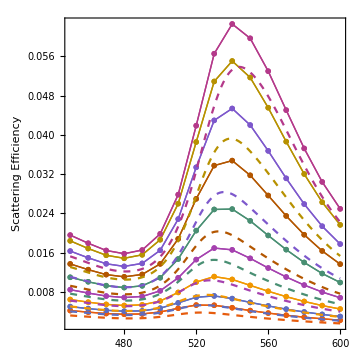
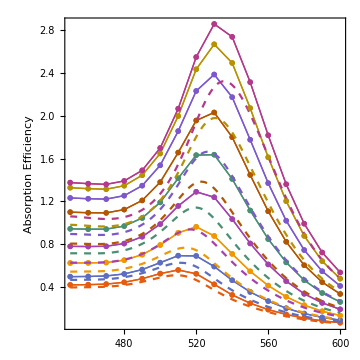
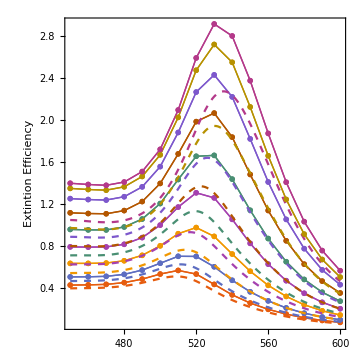

{Incrusted/Mie_FEM1.svg,Incrusted/Mie_FEM2.svg,Incrusted/Mie_FEM3.svg}

```mathematica
label = #<>"Efficiency"&/@{"Scattering ", "Absorption ", "Extintion "};
algo = Array[ListPlot[fromAir[[#1,#2]]/.{x_,y_}-> {x,1.*y},PlotStyle->Directive[colors[[#2]],Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True, Joined -> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],label[[#1]]},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->1]
&,{3,9}];

eff = Array[ ListPlot[{sca,ext,abs}[[#1,#2]],PlotStyle->(Directive[Dashed,colors[[#2]]]),Joined->True]&,{3,9}];

Show/@ MapThread[ Show[{#1,#2,#3},PlotRange-> All,AspectRatio-> 1]&,{algo,algo,eff},2]
Export[FileNameJoin[{"Incrusted","Mie_FEM"<>ToString[#]<>".svg"}],%[[#]]]&/@Range[3]
```

# Silicon NP

## Silicon NP 90nm

```mathematica
FileNames["*.csv","Silicon"];
data= Drop[Import[#,"Data"],5]&/@%;
TableForm[%%]
rad = 90(*nm*);
```

Silicon/Si_90nmMie.csv

### Convergencia

```mathematica
mieFem = data[[1,;;,{2,#}]]&/@{3,4,5};
```

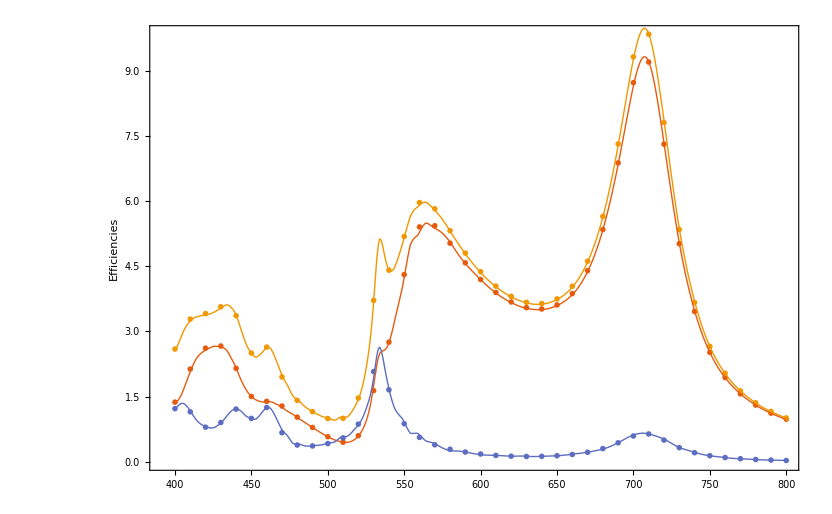

Silicon/Mie-FEM_Air.pdf

```mathematica
amp =1;
(*sca, abs, ext*)
order = {1,2,3};
scadata  = 1;

{scaMie,extMie} = Transpose[Table[Through[{scaQ,extQ}[{1.,nSiFunc[λ]},λ,rad]],{λ, 400,800}]];
Show[{ListPlot[If[#==scadata,mieFem[[#]]/.{x_,y_}-> {x,amp*y},mieFem[[#]]]&/@order,PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
PlotLegends->Placed[SwatchLegend[Automatic,MaTeX[{"Q_{sca}","Q_{abs}","Q_{ext}"},ContentPadding->False],LegendLayout->"Row",
				LegendLabel->LineLegend[{Black,Black},Style[#,texStyle]&/@{"Mie","FEM"},LegendLayout->"Row",LegendMarkers->{None,Graphics[Circle[]]},
						LegendLabel->Style["90 nm-SiNP@Air",texStyle]
						]],{Left,Top}]
,ImageSize-> Medium],
ListLinePlot[{scaMie*amp,extMie-scaMie,extMie},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"]}]
Export[FileNameJoin[{"Silicon","Mie-FEM_Air.pdf"}],%]
```

```mathematica
amp =50;
(*sca, abs, ext*)
order = {1,2,3};
scadata  = 1;

{scaSize,extSize} = Transpose[Table[Through[{scaQ,extQ}[{1.5,nAuSize[λ,5]},λ,rad]],{λ, 400,800}]];
Show[{ListPlot[If[#==scadata,miebk7[[#]]/.{x_,y_}-> {x,amp*y/1.5},miebk7[[#]]/.{x_,y_}-> {x,y/1.5}]&/@order,PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
PlotLegends->Placed[SwatchLegend[Automatic,MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],LegendLayout->"Row",
				LegendLabel->LineLegend[{Black,Black},Style[#,texStyle]&/@{"Mie","FEM"},LegendLayout->"Row",LegendMarkers->{None,Graphics[Circle[]]},
						LegendLabel->Style["12.5 nm-AuNP@BK7",texStyle]
						]],{Right,Bottom}]
,ImageSize-> 400,AspectRatio->1/2.5],
ListLinePlot[{scaSize*amp,extSize-scaSize,extSize},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"]}]
Export[FileNameJoin[{"SupportedNP","Mie-FEM_BK7.pdf"}],%]
```

-Graphics-

SupportedNP/Mie-FEM_BK7.pdf